# Vacuum Decay Rate

## Effective Potential in 1d

Plug in the vev condition for S and eliminate it.

```mathematica
ClearAll["Global`*"]
g=0.65;
gY=0.36;
yt=0.9945;
Q=150.;
mh=125.;
μH2[mS_,sinθ_]:=(mh^2 mS^2)/(2(sinθ^2 mh^2+(1-sinθ^2)mS^2));
μS2[mS_,sinθ_]:=sinθ^2 mh^2+(1-sinθ^2)mS^2;
A2[mS_,sinθ_]:=((mh^2-mS^2)^2 sinθ^2(1-sinθ^2))/(2 v^2);
λ[mS_,sinθ_]:=((1-sinθ^2)mh^2+sinθ^2 mS^2)/(4 v^2);
S[A_,μS_,h_]:=A/(2 μS^2)h^2;
V0[λ_,A_,μH_,μS_,h_]:=1/4 λ h^4-1/2 μH^2 h^2+1/2 μS^2 S[A,μS,h]^2-1/2 A S[A,μS,h] h^2;
mW[h_]:=1/4 g^2 h^2;
mZ[h_]:=1/4(g^2+gY^2)h^2;
mt[h_]:=1/2 yt^2 h^2;
mX[λ_,A_,μH_,μS_,h_]:=-μH^2-A S[A,μS,h]+λ h^2;
sqrt[λ_,A_,μH_,μS_,h_]:=√(A^2(4 h^2+ S[A,μS,h]^2)+2A S[A,μS,h](μH^2+μS^2-3λ h^2)+(μH^2+μS^2-3λ h^2)^2);
mH[λ_,A_,μH_,μS_,h_]:=1/2(-μH^2+μS^2-A S[A,μS,h]+3λ h^2+sqrt[λ,A,μH,μS,h]);
mS[λ_,A_,μH_,μS_,h_]:=1/2(-μH^2+μS^2-A S[A,μS,h]+3λ h^2-sqrt[λ,A,μH,μS,h]);
VCW[λ_,A_,μH_,μS_,h_]:=1/(64 π^2)(6 mW[h]^2(Log[mW[h]/Q^2]-5/6)+3 mZ[h]^2(Log[mZ[h]/Q^2]-5/6)+mH[λ,A,μH,μS,h]^2(Log[Abs[mH[λ,A,μH,μS,h]]/Q^2]-3/2)+3 mX[λ,A,μH,μS,h]^2(Log[Abs[mX[λ,A,μH,μS,h]]/Q^2]-3/2)-12 mt[h]^2(Log[mt[h]/Q^2]-3/2));
V0T[λ_,A_,μH_,μS_,h_]:=V0[λ,A,μH,μS,h]+VCW[λ,A,μH,μS,h]-(V0[λ,A,μH,μS,10^-3]+VCW[λ,A,μH,μS,10^-3]);
```

```mathematica
fitting=Table[{ϕ,V0T[0.125299,10.6204,20.2598,21.8138,ϕ]},{ϕ,10^-3,10000,1}];
```

86.6867

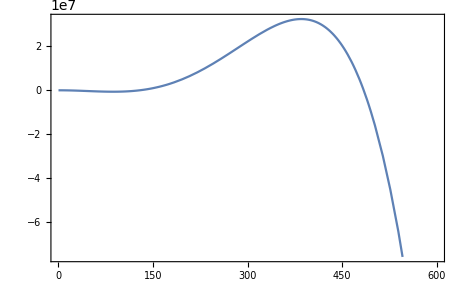

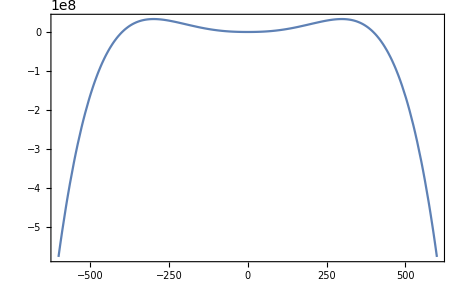

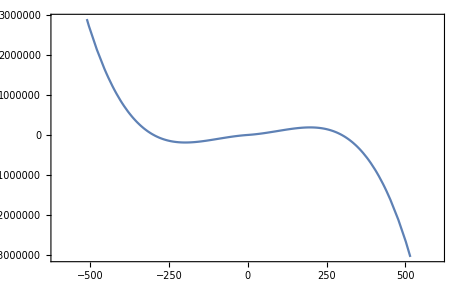

```mathematica
Vfit[ϕ_]=Interpolation[fitting][ϕ];
vev=ϕ/.FindMinimum[Vfit[ϕ],{ϕ,100}][[2]]
Vb[ϕ_]:=Vfit[ϕ+vev]-Vfit[vev]/;ϕ≥0;
Vb[ϕ_]:=Vfit[-ϕ+vev]-Vfit[vev]/;ϕ<0;
dVlog[lgϕ_]:=D[Vfit[ⅇ^y+vev],{{y}}]/.{y->lgϕ}/;lgϕ≥1;
dVlog[lgϕ_]:=D[Vfit[ⅇ^y+vev],{{y}}]/.{y->lgϕ}/;lgϕ<1;
dVfit[ϕ_]:=Vfit'[ϕ+vev]/;ϕ≥0;
dVfit[ϕ_]:=-Vfit'[-ϕ+vev]/;ϕ<0;
Plot[Vfit[ϕ],{ϕ,0,600}]
Plot[Vb[ϕ],{ϕ,-600,600}]
Plot[dVfit[ϕ],{ϕ,-600,600}]
```

```mathematica
FindMaximum[Vb[ϕ],{ϕ,400}]
```

{3.31499×10^7,{ϕ→298.26}}

```mathematica
FindMinimum[Vb[ϕ],{ϕ,100}]
```

{0.,{ϕ→-2.37025×10^-7}}

## Shooting

```mathematica
ϕIR=10^-3;
rIR=10^-3;
ranger=0.1;
shootinginitial=1000;
shootingfinal=10000;
δϕ0=10^3;
δϕ1=10^2;
δϕ2=10^1;
δϕ3=10^0;
δϕ4=10^-1;
δϕ5=10^-2;
δϕ6=10^-3;
δr=0.02*ranger;
```

```mathematica
overshoot‵trigger[escape0_]:=Catch[Do[If[NDSolveValue[{(ϕ''[r]+3/r ϕ'[r])-dVfit[ϕ[r]]==0,ϕ[rIR]==escape0
,ϕ'[rIR]==0},ϕ,{r,rIR,ranger}][t]<0,Throw[t]],{t,rIR,ranger,δr}]]
```

```mathematica
overshoot‵trigger[7000]
```

0.005

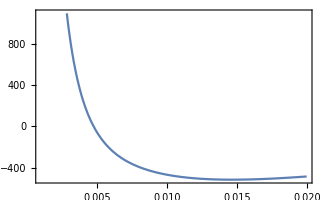

```mathematica
try[t_]=NDSolveValue[{(ϕ''[r]+3/r ϕ'[r])-dVfit[ϕ[r]]==0,ϕ[rIR]==5901.16
,ϕ'[rIR]==0},ϕ,{r,rIR,ranger}][t];
Plot[try[t],{t,rIR,0.02}]
```

```mathematica
initial00=Catch[Do[If[overshoot‵trigger[y0]>0,Throw[y0]],{y0,shootinginitial,shootingfinal,δϕ0}]];
initial11=Catch[Do[If[overshoot‵trigger[y0]>0,Throw[y0]],{y0,initial00-δϕ0,shootingfinal,δϕ1}]];
initial22=Catch[Do[If[overshoot‵trigger[y0]>0,Throw[y0]],{y0,initial11-δϕ1,shootingfinal,δϕ2}]];
initial33=Catch[Do[If[overshoot‵trigger[y0]>0,Throw[y0]],{y0,initial22-δϕ2,shootingfinal,δϕ3}]];
initial44=Catch[Do[If[overshoot‵trigger[y0]>0,Throw[y0]],{y0,initial33-δϕ3,shootingfinal,δϕ4}]];
initial55=Catch[Do[If[overshoot‵trigger[y0]>0,Throw[y0]],{y0,initial44-δϕ4,shootingfinal,δϕ5}]];
initial66=Catch[Do[If[overshoot‵trigger[y0]>0,Throw[y0]],{y0,initial55-δϕ5,shootingfinal,δϕ6}]]
```

1475291/250

```mathematica
initial66//N
```

5901.16

```mathematica
rinfty[initialf_]:=Catch[Do[If[NDSolveValue[{(ϕ''[r]+3/r ϕ'[r])-dVfit[ϕ[r]]==0,ϕ[rIR]==initialf
,ϕ'[rIR]==0},ϕ,{r,rIR,ranger}][t]<0,Throw[t]],{t,rIR,ranger,δr}]];
bounceaction[initial_,rinf_]:=NIntegrate[Evaluate[2π r^3(1/2 ϕ'[r]*ϕ'[r]+Vb[ϕ[r]])/.NDSolve[{(ϕ''[r]+3/r ϕ'[r])-dVfit[ϕ[r]]==0,ϕ[rIR]==initial
,ϕ'[rIR]==0},ϕ,{r,rIR,rinf}]],{r,rIR,rinf}]
rinfty[initial66]
```

0.0198

```mathematica
bounceaction[initial66,rinfty[initial66]]
```

{217.114}

## Shooting with semi-analytical potential

Scalar contributions are neglected here for simplicity. This approximation allows us for using analytical method to write down the ⅆV/ⅆh.

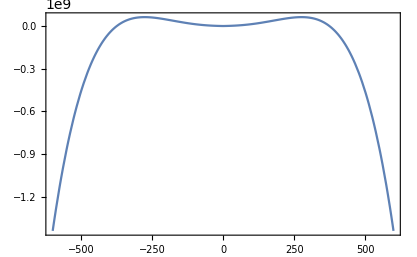

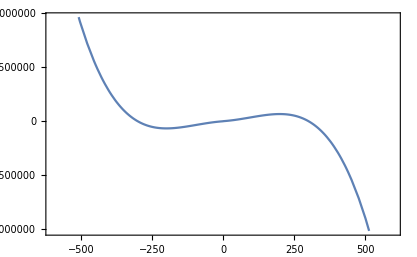

```mathematica
VCW‵approx[λ_,A_,μH_,μS_,h_]:=1/(64 π^2)(6 mW[h]^2(Log[mW[h]/Q^2]-5/6)+3 mZ[h]^2(Log[mZ[h]/Q^2]-5/6)-12 mt[h]^2(Log[mt[h]/Q^2]-3/2));
Vapprox[λ_,A_,μH_,μS_,h_]:=VCW‵approx[λ,A,μH,μS,h]+V0T[λ,A,μH,μS,h]-(VCW‵approx[λ,A,μH,μS,10^-3]+V0T[λ,A,μH,μS,10^-3]);
Vb‵approx[h_]:=Vapprox[0.125299,10.6204,20.2598,21.8138,h+vev]-Vapprox[0.125299,10.6204,20.2598,21.8138,vev]/;h≥0;
Vb‵approx[h_]:=Vapprox[0.125299,10.6204,20.2598,21.8138,-h+vev]-Vapprox[0.125299,10.6204,20.2598,21.8138,vev]/;h<0;
dV0dh[λ_,A_,μH_,μS_,h_]:=λ h^3-μH^2 h+S[A,μS,h]A h-A S[A,μS,h]h-1/2 A^2/μS^2 h^3;
dVCWdh[λ_,A_,μH_,μS_,h_]:=1/(64 π^2)(6(mW[h]mW'[h](2Log[mW[h]/Q^2]-5/3+1))+3(mZ[h]mZ'[h](2Log[mZ[h]/Q^2]-5/3+1))-12(mt[h]mt'[h](2Log[mt[h]/Q^2]-3+1)));
dVdh[λ_,A_,μH_,μS_,h_]:=dV0dh[λ,A,μH,μS,h]+dVCWdh[λ,A,μH,μS,h];
dVdhbounce[h_]:=dVdh[0.125299,10.6204,20.2598,21.8138,h+vev]/;h≥0;
dVdhbounce[h_]:=-dVdh[0.125299,10.6204,20.2598,21.8138,-h+vev]/;h<0;
Plot[Vb‵approx[h],{h,-600,600}]
Plot[dVdhbounce[h],{h,-600,600}]
```

### Using regular equation

```mathematica
ϕIR=10^-5;
rIR=10^-5;
ranger=0.002;
shootinginitial=100000;
shootingfinal=300000;
δϕ0=10^4;
δϕ1=10^3;
δϕ2=10^2;
δϕ3=10^1;
δϕ4=10^0;
δϕ5=10^-1;
δϕ6=10^-2;
δr=0.02*ranger;
```

```mathematica
overshoot‵trigger‵approx[escape0_]:=Catch[Do[If[NDSolveValue[{(ϕ''[r]+3/r ϕ'[r])-dVdhbounce[ϕ[r]]==0,ϕ[rIR]==escape0
,ϕ'[rIR]==0},ϕ,{r,rIR,ranger}][t]<0,Throw[t]],{t,rIR,ranger,δr}]]
```

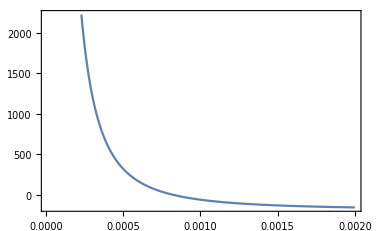

```mathematica
try[t_]=NDSolveValue[{(ϕ''[r]+3/r ϕ'[r])-dVdhbounce[ϕ[r]]==0,ϕ[rIR]==220000
,ϕ'[rIR]==0},ϕ,{r,rIR,ranger}][t];
Plot[try[t],{t,rIR,0.002}]
```

```mathematica
initial00=Catch[Do[If[overshoot‵trigger‵approx[y0]>0,Throw[y0]],{y0,shootinginitial,shootingfinal,δϕ0}]]
initial11=Catch[Do[If[overshoot‵trigger‵approx[y0]>0,Throw[y0]],{y0,initial00-δϕ0,shootingfinal,δϕ1}]]
initial22=Catch[Do[If[overshoot‵trigger‵approx[y0]>0,Throw[y0]],{y0,initial11-δϕ1,shootingfinal,δϕ2}]]
initial33=Catch[Do[If[overshoot‵trigger‵approx[y0]>0,Throw[y0]],{y0,initial22-δϕ2,shootingfinal,δϕ3}]]
initial44=Catch[Do[If[overshoot‵trigger‵approx[y0]>0,Throw[y0]],{y0,initial33-δϕ3,shootingfinal,δϕ4}]]
initial55=Catch[Do[If[overshoot‵trigger‵approx[y0]>0,Throw[y0]],{y0,initial44-δϕ4,shootingfinal,δϕ5}]]
initial66=Catch[Do[If[overshoot‵trigger‵approx[y0]>0,Throw[y0]],{y0,initial55-δϕ5,shootingfinal,δϕ6}]]
```

220000

219000

218300

218270

218267

1091333/5

5456663/25

```mathematica
rinfty[initialf_]:=Catch[Do[If[NDSolveValue[{(ϕ''[r]+3/r ϕ'[r])-dVdhbounce[ϕ[r]]==0,ϕ[rIR]==initialf
,ϕ'[rIR]==0},ϕ,{r,rIR,ranger}][t]<0,Throw[t]],{t,rIR,ranger,δr}]];
bounceaction[initial_,rinf_]:=NIntegrate[Evaluate[2π r^3(1/2 ϕ'[r]*ϕ'[r]+Vb‵approx[ϕ[r]])/.NDSolve[{(ϕ''[r]+3/r ϕ'[r])-dVdhbounce[ϕ[r]]==0,ϕ[rIR]==initial
,ϕ'[rIR]==0},ϕ,{r,rIR,rinf}]],{r,rIR,rinf}]
rinfty[initial66]
```

0.00197

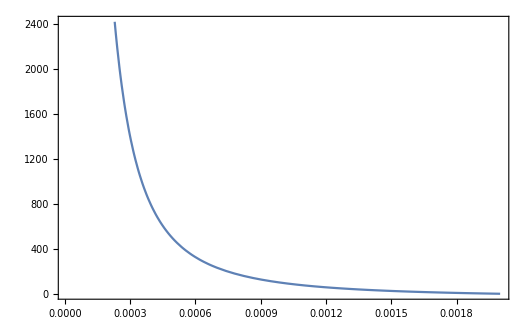

```mathematica
sol[t_]=NDSolveValue[{(ϕ''[r]+3/r ϕ'[r])-dVdhbounce[ϕ[r]]==0,ϕ[rIR]==initial66
,ϕ'[rIR]==0},ϕ,{r,rIR,ranger}][t];
Plot[sol[t],{t,rIR,0.002}]
```

```mathematica
bounceaction[initial66,rinfty[initial66]]
```

{3.84401}

### Using exponential expression for the bounce equation

```mathematica
ϕIR=10^-5;
rIR=10^-5;
ranger=0.0015;
shootinginitial=100000;
shootingfinal=300000;
δϕ0=10^4;
δϕ1=10^3;
δϕ2=10^2;
δϕ3=10^1;
δϕ4=10^0;
δϕ5=10^-1;
δϕ6=10^-2;
δr=0.02*ranger;
```

```mathematica
dVdhexp[y_]:=dVdhbounce[ⅇ^y];
```

Use exponential expression: ϕ→ⅇ^y,r→ⅇ^x:

```mathematica
overshoot‵trigger‵approx[logescape_]:=(
sol[t_]:=NDSolveValue[{(ⅇ^(y[x]-2x)(y''[x]+y'[x]*y'[x]-y'[x])+3/ⅇ^x ⅇ^(y[x]-x)y'[x])-dVdhexp[y[x]]==0,y[Log[rIR]]==logescape
,y'[Log[rIR]]==0},y,{x,Log[rIR],Log[ranger]}][t];
Catch[Do[If[sol[Log[t]]≤ⅇ,Throw[t]],{t,rIR,ranger,δr}]]
)
```

```mathematica
initial00=Catch[Do[If[overshoot‵trigger‵approx[Log[y0]]>0,Throw[y0]],{y0,shootinginitial,shootingfinal,δϕ0}]]
initial11=Catch[Do[If[overshoot‵trigger‵approx[Log[y0]]>0,Throw[y0]],{y0,initial00-δϕ0,shootingfinal,δϕ1}]]
initial22=Catch[Do[If[overshoot‵trigger‵approx[Log[y0]]>0,Throw[y0]],{y0,initial11-δϕ1,shootingfinal,δϕ2}]]
initial33=Catch[Do[If[overshoot‵trigger‵approx[Log[y0]]>0,Throw[y0]],{y0,initial22-δϕ2,shootingfinal,δϕ3}]]
initial44=Catch[Do[If[overshoot‵trigger‵approx[Log[y0]]>0,Throw[y0]],{y0,initial33-δϕ3,shootingfinal,δϕ4}]]
initial55=Catch[Do[If[overshoot‵trigger‵approx[Log[y0]]>0,Throw[y0]],{y0,initial44-δϕ4,shootingfinal,δϕ5}]]
initial66=Catch[Do[If[overshoot‵trigger‵approx[Log[y0]]>0,Throw[y0]],{y0,initial55-δϕ5,shootingfinal,δϕ6}]]
```

NDSolveValue::ndsz: At x == -7.10848, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolveValue::ndsz will be suppressed during this calculation.

220000

NDSolveValue::ndsz: At x == -6.77688, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolveValue::ndsz will be suppressed during this calculation.

219000

218400

218390

218385

2183847/10

4367693/20

NDSolveValue::ndsz: At x == -6.77688, step size is effectively zero; singularity or stiff system suspected.

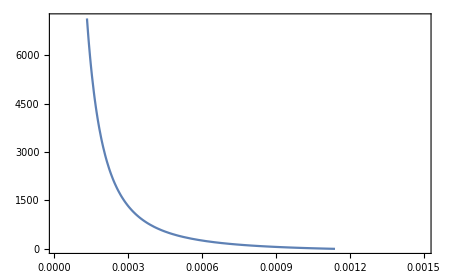

```mathematica
tryy[t_]:=NDSolveValue[{(ⅇ^(y[x]-2x)(y''[x]+y'[x]*y'[x]+2y'[x]))-dVdhexp[y[x]]==0,y[Log[rIR]]==Log[219000]
,y'[Log[rIR]]==0},y,{x,Log[rIR],Log[ranger]}][t]
Plot[Exp[tryy[Log[r]]],{r,rIR,0.0015}]
```

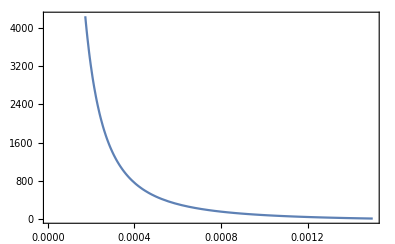

```mathematica
finalsol[t_]:=NDSolveValue[{(ⅇ^(y[x]-2x)(y''[x]+y'[x]*y'[x]+2y'[x]))-dVdhexp[y[x]]==0,y[Log[rIR]]==Log[initial66]
,y'[Log[rIR]]==0},y,{x,Log[rIR],Log[ranger]}][t];
Plot[Exp[finalsol[Log[r]]],{r,rIR,0.0015}]
```

```mathematica
overshoot‵trigger‵approx[219000]
```

```mathematica
rinfty[initialf_]:=(
sol[t_]:=NDSolveValue[{(ⅇ^(y[x]-2x)(y''[x]+y'[x]*y'[x]-y'[x])+3/ⅇ^x ⅇ^(y[x]-x)y'[x])-dVdhexp[y[x]]==0,y[Log[rIR]]==Log[initialf]
,y'[Log[rIR]]==0},y,{x,Log[rIR],Log[ranger]}][t];
Catch[Do[If[sol[Log[t]]≤ⅇ,Throw[t]],{t,rIR,ranger,δr}]]
);
bounceaction[initial_,rinf_]:=(
ysol[t_]:=NDSolveValue[{(ⅇ^(y[x]-2x)(y''[x]+y'[x]*y'[x]+2y'[x]))-dVdhexp[y[x]]==0,y[Log[rIR]]==Log[initial]
,y'[Log[rIR]]==0},y,{x,Log[rIR],Log[ranger]}][t];
bounceϕ[r_]:=Exp[ysol[Log[r]]];
NIntegrate[2π r^3(1/2 bounceϕ'[r]*bounceϕ'[r]+Vb‵approx[bounceϕ[r]]),{r,rIR,rinf}])
rinfty[initial66]
```

0.00148

```mathematica
bounceaction[initial66,rinfty[initial66]]
```

3.26863